2. Introduction
(a)The syntax of the Mathematica language:

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m;
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

(b) The meaning of expressions:

(c) The four kinds of bracketing in Mathematica:

(d) Use Brackets and Braces Correctly:

```mathematica
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

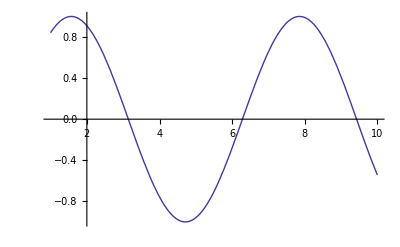

```mathematica
Plot[Sin[x],{x,1,10}]
```

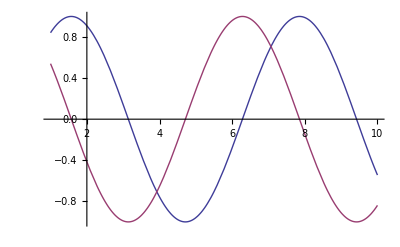

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

3. Symbolic Analysis
(a) Symbolic Computation:

```mathematica
-1+2 x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4 x^2
```

x-3 x^2

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
3+62-1;
Expand[%];
Factor[%]
```

64

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
Factor[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
Log[1+Cos[x]]
```

Log[1+Cos[x]]

(b) Values for Symbols:

```mathematica
1+2 x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x->3+y
```

x→3+y

```mathematica
x->3+y;
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
x=3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1+a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
x+5-2 x
```

6+a-2 (1+a)

```mathematica
x=.
```

```mathematica
x+5-2 x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5 a
```

1+25 a^2

```mathematica
t/.x->Pi//N
```

10.8696

(c) Transforming Algebraic Expressions:

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Expand[(1+x)^2];
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Expand[(1+x+3 y)^4];
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

(d) Simplifying Algebraic Expressions:

```mathematica
Simplify[x^2+2 x+1]
```

(1+x)^2

```mathematica
Simplify[x^10-1]
```

-1+x^10

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
Simplify[x^2+2 x+1];
D[%,x];
Simplify[%]
```

2 (1+x)

```mathematica
Simplify[x^2+2 x+1];
D[%,x];
```

```mathematica
Simplify[Gamma[x] Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x] Gamma[1-x]]
```

π Csc[π x]

4. Calculus
(a) Differentiation:

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
D[x^2+y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2+y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
D[x^2+y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
D[{x^2+y^2,x y},{{x,y}}]
```

{{2 x,2 y},{y,x}}

(b) How to plot functions of one variable:

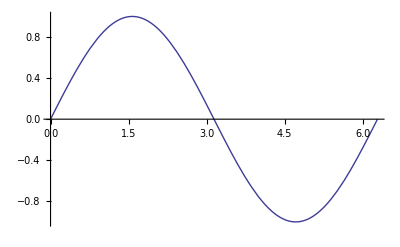

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

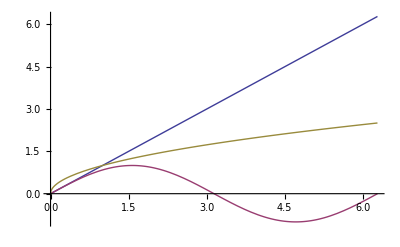

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

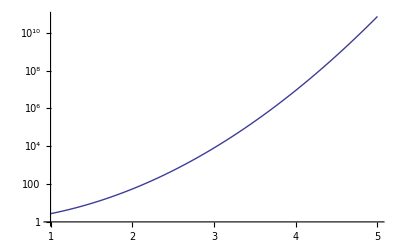

```mathematica
LogPlot[E^x^2,{x,1,5}]
```

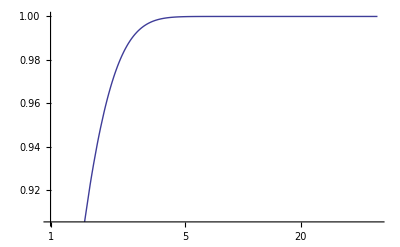

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

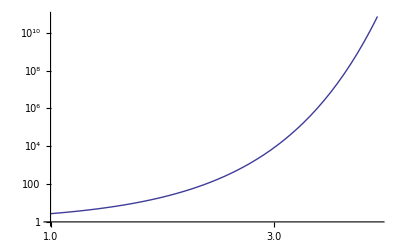

```mathematica
LogLogPlot[E^x^2,{x,1,5}]
```

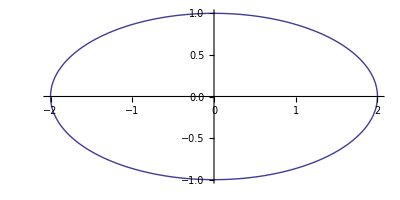

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

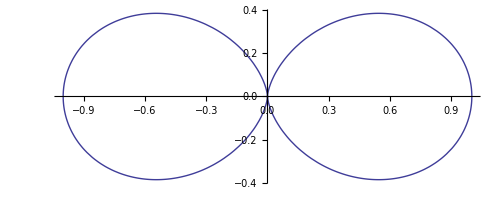

```mathematica
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
```

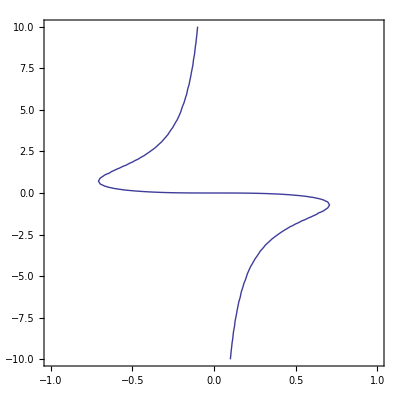

```mathematica
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}]
```

(c) How to plot parametric functions:

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
```

-Graphics-

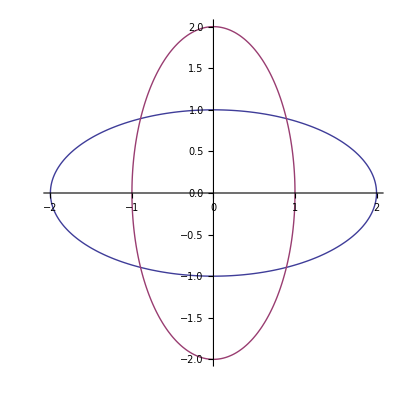

```mathematica
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]}},{t,0,2 Pi}]
```

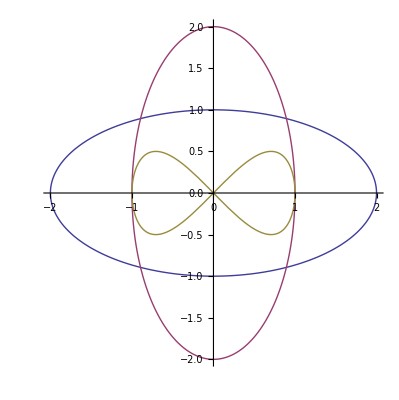

```mathematica
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]},{Sin[t],Sin[t] Cos[t]}},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],Log[r^(1/2)]},{r,0.1,1},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

(d) How to plot the results of NDSolve:

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
```

```mathematica
sol=NDSolve[ode1,y,{x,-10,10}]
```

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

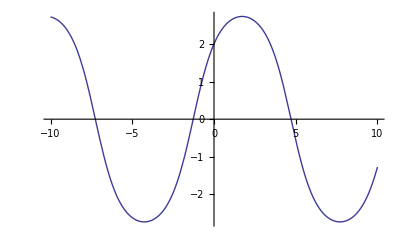

```mathematica
Plot[y[x]/.sol,{x,-10,10}]
```

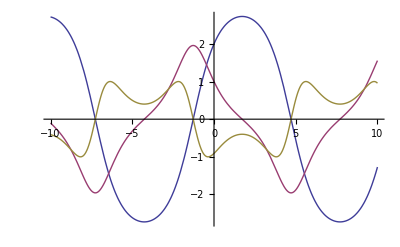

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}]
```

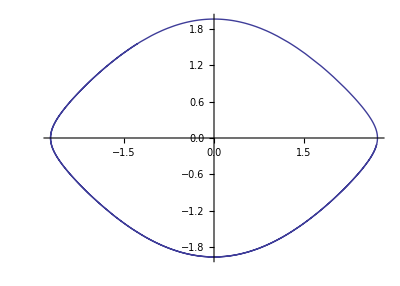

```mathematica
ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,-10,10}]
```

```mathematica
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

```mathematica
Plot3D[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

-Graphics3D-

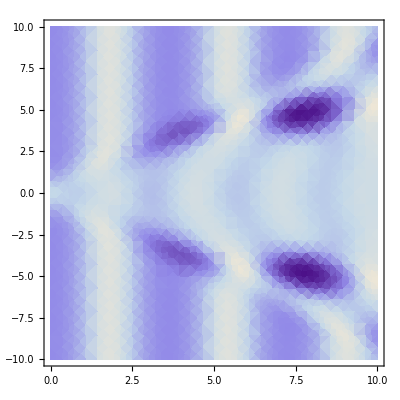

```mathematica
DensityPlot[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

```mathematica
plots=Table[Plot[u[t,x]/.wws,{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
bg = NDSolve[{D[u[t], t,t] == (1 - u[t]^2) (1 + 2 u[t]), u[0] == 0, u'[0] == 0}, 
  u, {t, 0, 10}]
```

{{u→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
plots=Table[Plot[(u[t,x]/.wws)-(u[t]/.bg),{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
```

```mathematica
ListAnimate[plots]
```

6. Manipulate
Follow the tutorial up to and including the section \Beautifying the control area”:

```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{n2,1,20}]
```

```mathematica
Manipulate[Plot[a1 Sin[n1 (x+p1)]+a2 Sin[n2 (x+p2)],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{p1,0,2 Pi},{n2,1,20},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20}]
```

```mathematica
Manipulate[n,{n,1,20,1}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20,1}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,300,1}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,1/2,1/3,1/144},{m,1/2,1/3,1/144}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,a,10 a,a/12},{m,a,10 a,a/12}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Frame->frame,PlotRange->2],{n1,1,20},{n2,1,20},{frame,{True,False}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,2,1,0,-1,-2},ControlType->SetterBar}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1},ControlType->Manipulator}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,2,1.5,1,0.5,0,-0.5,-1,-1.5,-2}},{filling,-2,2}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{a1,0,1},{p1,0,2 Pi},{n2,1,4},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{{a1,1},0,1},{p1,0,2 Pi},{{n2,5/4},1,4},{{a2,1},0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{n2,5/4,"Frequency 2"},1,4},Delimiter,{{a1,1,"Amplitude 1"},0,1},{{a2,1,"Amplitude 2"},0,1},Delimiter,{{p1,0,"Phase 1"},0,2 Pi},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],"Horizontal",{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,"Vertical",{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[pt,{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[{PointSize[0.1],Point[pt]},PlotRange->1],{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[ParametricPlot[{a[[1]] Sin[n[[1]] (x+p[[1]])],a[[2]] Cos[n[[2]] (x+p[[2]])]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n,{1,5/4},"Frequency"},{1,1},{4,4}},{{a,{1,1},"Amplitude"},{0,0},{1,1}},{{p,{0,0},"Phase"},{0,0},{2 Pi,2 Pi}},ControlPlacement->Left]
```

```mathematica
Manipulate[Graphics[{PointSize[0.1],Point[pt]},PlotRange->1],{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[{Line[Table[{{Cos[t],Sin[t]},pt},{t,2. Pi/n,2. Pi,2. Pi/n}]]},PlotRange->1],{{n,30},1,200,1},{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[Line[Table[{{Sin[n+i],Cos[n+i]},{Sin[n+dn+i],Cos[n+dn+i]}},{i,0,di,di/l}]],PlotRange->1.1],{n,0,2 π},{dn,0,2 π},{di,1,2 π},{l,1,200},ControlPlacement->Left]
```

```mathematica
Manipulate[Graphics[{Line[Table[{{Cos[t],Sin[t]},pt},{t,2. Pi/n,2. Pi,2. Pi/n}]]},PlotRange->1],{{n,30},1,200,1},{{pt,{0,0}},Locator}]
```

```mathematica
Manipulate[Graphics[Polygon[{pt1,pt2,pt3}],PlotRange->1],{{pt1,{0,0}},Locator},{{pt2,{0,1}},Locator},{{pt3,{1,0}},Locator}]
```

```mathematica
Manipulate[Graphics[Polygon[pts],PlotRange->1],{{pts,{{0,0},{1,0},{0,1}}},Locator}]
```

```mathematica
Manipulate[Graphics[Polygon[pts],PlotRange->1],{{pts,{{0,0},{.5,0},{0,.5}}},Locator,LocatorAutoCreate->True}]
```

```mathematica
Manipulate[Graphics[{FaceForm[face],EdgeForm[{edge,Thickness[thickness]}],Polygon[pts]},PlotRange->1,Background->background],{face,Green},{edge,Red},{background,Cyan},{{thickness,0.02},0,0.1},{{pts,{{0,0},{.5,0},{0,.5}}},Locator,LocatorAutoCreate->True}]
```

```mathematica
Manipulate[Module[{x},Plot[Fit[points,Table[x^i,{i,0,order}],x],{x,-2,2},PlotRange->2,ImageSize->500,Evaluated->True]],{{order,3},1,10,1,Appearance->"Labeled"},{{points,RandomReal[{-2,2},{5,2}]},Locator,LocatorAutoCreate->True}]
```

```mathematica
Manipulate[Plot[InterpolatingPolynomial[points,x],{x,-2,2},PlotRange->2],{{points,RandomReal[{-2,2},{5,2}]},Locator}]
```

```mathematica
Manipulate[Plot3D[Sin[n x y],{x,0,3},{y,0,3}],{n,1,5}]
```

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0},r1],Sphere[{c[[1]],c[[2]],0},r2]},PlotRange->2],{{r1,1},0,2},{{r2,1},0,2},{c,{-2,-2},{2,2}}]
```

```mathematica
Manipulate[SphericalPlot3D[θ+ϕ,{θ,0,a π},{ϕ,0,b π},SphericalRegion->True,PlotRange->10,Ticks->None,BaseStyle->Opacity[opacity]],{a,0.1,2},{b,0.1,2},{opacity,1,0}]
```

```mathematica
Manipulate[Grid[Table[{i,i^m},{i,1,n}],Alignment->Left,Frame->All],{n,1,20,1},{m,1,100,1}]
```

```mathematica
Manipulate[Column[{{style,size},Slider[0.5,Appearance->{style,size}]}],{style,{"Automatic","Vertical","LeftArrow","RightArrow","UpArrow","DownArrow"},ControlType->Slider},{size,{"Automatic","Tiny","Small","Medium","Large"},ControlType->Slider}]
```

```mathematica
Manipulate[TabView[Table[Nest[1/(1-#)&,base,i],{i,1,n}],Dynamic[pane],Alignment->alignment],{n,1,20,1},{alignment,{-1,-1},{1,1}},{pane,1,n,1}]
```

```mathematica
f[x_]:=x^2
```

```mathematica
Manipulate[f[y],{y,0,100}]
```

```mathematica
g[x_]:=x^2
```

```mathematica
Manipulate[g[y],{y,0,100},SaveDefinitions->True]
```

```mathematica
Manipulate[h[y],{y,0,100},Initialization:>(h[x_]:=x^2)]
```

```mathematica
Manipulate[Plot[a1 Sin[n1 x]+a2 Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{n2,1,20},{a2,0,1}]
```

```mathematica
Manipulate[Plot[a1 Sin[n1 x]+a2 Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{n2,1,20},{a2,0,1},ControllerMethod->"Absolute"]
```

```mathematica
Manipulate[Graphics[{Thickness[0.02],Line[{{-Cos[l],Sin[l]},{0,0},{Cos[l],Sin[l]}}],Line[{{0,0},{0,1.5}}],Line[{{-Cos[a],1+Sin[a]},{0,1},{Cos[a],1+Sin[a]}}],Disk[{0,1.5},.2]},PlotRange->{{-1,1},{-1,2}}],{l,-Pi/2,0},{a,-Pi/2,Pi/2},ControllerMethod->"Absolute"]
```

```mathematica
ControllerManipulate[Graphics[{Thickness[0.02],Line[{{-Cos[l],Sin[l]},{0,0},{Cos[l],Sin[l]}}],Line[{{0,0},{0,1.5}}],Line[{{-Cos[a],1+Sin[a]},{0,1},{Cos[a],1+Sin[a]}}],Disk[{0,1.5},.2]},PlotRange->{{-1,1},{-1,2}}],{l,-Pi/2,0},{a,-Pi/2,Pi/2},ControllerMethod->"Absolute"]
```

```mathematica
Manipulate[Graphics[{PointSize[0.05],Point[pt]},PlotRange->1],{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[{If[b1,Red,Green],PointSize[0.05],Point[pt]},PlotRange->1],{pt,{-1,-1},{1,1}},{b1,{True,False}}]
```

```mathematica
Manipulate[Graphics[{If[b1,Red,Green],PointSize[0.05],Point[pt]},PlotRange->1],{pt,{-1,-1},{1,1}},{b1,{True,False}},ControllerMethod->"Absolute"]
```

```mathematica
Manipulate[x,"X"->{x,0,1}]
```

```mathematica
Manipulate[x,"X2"->{x,0,1}]
```

```mathematica
Manipulate[Graphics[{PointSize[0.05],Point[pt]},PlotRange->1],"XY"->{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics3D[{PointSize[0.05],Point[pt]},PlotRange->1],"XYZ"->{pt,{-1,-1,-1},{1,1,1}}]
```

```mathematica
Manipulate[Graphics3D[{Thickness[0.01],PointSize[0.04],Point[pt1],Line[{pt1,pt1+pt2}]},PlotRange->1],"XYZ"->{pt1,{-1,-1,-1},{1,1,1}},"XYZ2"->{pt2,{-1,-1,-1},{1,1,1}},ControllerMethod->"Absolute"]
```

```mathematica
Manipulate[Graphics[{PointSize[0.05],Point[pt]},PlotRange->1],"XY3"->{pt,{-1,-1},{1,1}}]
```

```mathematica
ControllerInformation[]
```

```mathematica
ControllerInformation[]
```

```mathematica
Manipulate[Graphics[{PointSize[0.05],Point[{x,y}]},PlotRange->1],"X"->{x,-1,1},"YAbsolute"->{y,-1,1}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}},AutorunSequencing->All]
```

```mathematica
Manipulate[{w,x,y,z},{w,0,1},{x,0,1},{y,0,1},{z,0,1},AutorunSequencing->{3,1,4}]
```

```mathematica
Manipulate[{w,x,y,z},{w,0,1},{x,0,1},{y,0,1},{z,0,1},AutorunSequencing->{{1,2},{3,2},{4,10}}]
```

```mathematica
Manipulate[{x,y,z},{x,0,1},{y,0,1},{z,0,1}]
```